# Chapter. Solving partial differential equations

Mathematica preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->1,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12], 
     Cell[TextData[{"Solving partial differential equations"}], FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Boundary Conditions","Separation of Variables","Transforming variables","Integral Transform Methods","Summary"},#]&)]], 
FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];(*allows the creation of new symbols*)
```

```mathematica
ClearNotations[]
Symbolize[Subscript[A, _]];
Symbolize[c^_];
Symbolize[Subscript[b, _]];
```

```mathematica
SetOptions[Plot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial", 10, Plain],
Frame->True,
GridLines->None,
ImageSize-> 288,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial", 10, Plain],
Frame->True,
GridLines->None,
ImageSize->288,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[
Table[{x,Which[
Chop[x]==0,0,
0<x≤0.005,NumberForm[x,{2,3},NumberPadding->{"","0"}],
0.005<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
option1={
PlotRange->{{0,1},{0,1.05}},
FrameTicks->{ticks1[0,1,.2,5],ticks1[0,1,.2,5],ticks2[0,1,.2,5],ticks2[0,1,.2,5]},
FrameLabel->{"x/L","c/c^✶",None,None},
RotateLabel-> False};
```

```mathematica
option2={
PlotRange->{{0,.003},{0,1.05}},
FrameTicks->{ticks1[0,0.004,.001,5],ticks1[0,1,.2,5],ticks2[0,0.004,.001,5],ticks2[0,1,.2,5]},
FrameLabel->{"x (cm)","c/c^✶",None,None},
RotateLabel-> False};
```

```mathematica
option3={
PlotStyle-> {{Black,AbsolutePointSize[3]}},
PlotJoined-> False,
PlotRange->{{0,.003},{0,1.05}},
FrameTicks->{ ticks1[0,0.004,.001,5], ticks1[0,1,.2,5], ticks2[0,0.004,.001,5],ticks2[0,1,.2,5]},
FrameLabel->{"x (cm)","c/c^✶",None,None},
RotateLabel-> False};
```

```mathematica
(*Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i_[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;

Protect[InverseLaplaceTransform];*)
```

Mathematica Version 4.0 and above

To solve problems using Laplace transforms with Mathematica users of versions of Mathematica versions below 4.0 first need to load the package LaplaceTransform.m which is located in the Calculus subdirectory of the StandardPackages subdirectory in the directory AddOns. To get version 4.0 and higher to run identically to version 3.0 execute the work around in the cell below at the beginning of all notebooks which use Laplace transform. This was written by Lou D’Andria of Wolfram.

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

Partial differential equations (PDEs) come in many categories or classes. It is important to define these classes because the methods that have been developed to analytically solve PDEs generally apply only to certain classes. The classification of PDEs is:
1. The order of a PDE is the order of the highest derivative, for example

(∂c)/(∂t)=(∂^2 c)/(∂x^2)

is a second order PDE.
2. The number of independent variables, for example eqn (Chapter.EquationNumbered) has two, x and t.
3. PDEs are considered to be either linear or nonlinear depending on whether or not the dependent variable and all its derivatives appear in a linear fashion. The following equation

A(∂^2 c)/(∂x^2)+B(∂^2 c)/(∂x∂t)+C(∂^2 c)/(∂t^2)+D(∂c)/(∂x)+E(∂c)/(∂t)+Fc=G

is linear if A, B, C, D, E, F, and G are either constants or functions of x and t but not functions of c, otherwise it is nonlinear.
4. PDEs are homogeneous if G is zero for all x and t otherwise they are nonhomogeneous.
5. If the coefficients A, B, C, D, E, F, and G are constants the PDE is said to have constant coefficients otherwise variable coefficients.
6. Linear PDEs are further classified as being either parabolic, hyperbolic or elliptic based on the coefficients. Parabolic equations satisfy the relationship B^2-4AC=0, hyperbolic equations B^2-4AC >0, and elliptic equations B^2-4AC<0.
Some categories of PDEs of interest to electrochemists are parabolic equations with the form:

(∂^2 c)/(∂x^2)-(∂c)/(∂t)=0

which is a linear second order homogeneous parabolic PDE with constant coefficients;

(∂^2 c)/(∂x^2)-(∂c)/(∂t)-kc=0

which is a linear second order homogeneous parabolic PDE with constant coefficients; and

(∂^2 c)/(∂x^2)-(∂c)/(∂t)-k c^2=0

which is a nonlinear second order homogeneous parabolic PDE with constant coefficients.

These parabolic equations have a derivative that is second order with respect to one variable, x, which in electrochemistry is the distance from to the electrode surface, and first order with respect to another variable t, time. Parabolic equations are relatively common to many fields of science, engineering and, finance. Many methods are available for their solution. In this chapter analytical solutions to PDEs will be discussed in order to demonstrate the symbolic use of Mathematica.

## Chapter.Section Boundary Conditions

Solving parabolic PDEs requires an initial condition at t=0 and two boundary conditions. Boundary conditions are categorized as being of the first kind, the second kind or a mixture of both. Boundary conditions of the first kind, known as Dirichlet boundary conditions, are conditions that specify the solution at the boundary. For example in an electrochemical problem a Dirichlet boundary condition would be one in which the concentration of the electroactive species is specified at the electrode surface. Boundary conditions of the second kind, known as Neumann boundary conditions, are conditions that specify the derivative of the solution at the boundary. For example in an electrochemical problem a Neumann boundary condition would be one in which the flux of the electroactive species is specified at the electrode surface or some other boundary.
In an electrochemical experiment the initial condition is often that the concentration at the electrode surface, x=0, at t=0 is equal to the bulk concentration. In an electrochemical experiment in which the boundary conditions are said to be semi-infinite the first boundary condition reflects the fact that at infinite distances from the electrode surface the concentration is equal to the bulk concentration at all times. In practice this assumption holds for distances a long way from the surface relative to the thickness of the diffusion layer. The second boundary condition describes the concentration at the electrode surface and is dependant on the electrochemical method being employed. The initial condition and the first boundary conditions can be summarized as

c(x,0)=c^*

c(∞,t)=c^*

The second boundary condition depends on the electrochemical method being employed.

## Chapter.Section Separation of Variables

Chapter.Section.Subsection Homogeneous Boundary Conditions

The method of separation of variables assumes that the function c(x,t) can be represented as a product of two other functions X(x) and T(t). This method can be applied to PDEs that are linear and homogeneous and have boundary conditions of the form

α(∂c(x,t))/(∂x)+β c(0,t)=0

ω(∂c(L,t))/(∂x)+γ c(L,t)=0

where α, β, ω, and γ are constants and L is a boundary. Let’s consider Fick’s second law:

(∂c(x,t))/(∂t)=D(∂^2 c(x,t))/(∂x^2)

To solve Fick’s second law using separation of variables we begin by letting

c(x,t)=X(x)T(t)

```mathematica
ClearAll[λ,𝒟,T,X,t,x,c];

c[x_,t_]:=X[x]*T[t]
```

therefore eqn (Chapter.EquationNumbered) becomes

```mathematica
D[c[x,t],t]==𝒟*D[c[x,t],{x,2}]
```

X[x] T'[t]==𝒟 T[t] X''[x]

X(x)(∂T(t))/(∂t)=T(t)D(∂^2 X(x))/(∂x^2)

This equation is rearranged with X(x) and T(t) on separate sides

1/(T(t)D)(∂T(t))/(∂t)=1/(X(x))(∂^2 X(x))/(∂x^2)=-λ^2

Since t and x are independent of each other both sides of eqn (Chapter.EquationNumbered) must equal a constant, -λ^2. The constant, -λ^2, must be negative otherwise T(t) doesn’t go to zero as t → ∞. The other constraint is that λ ≠ 0. Equation (Chapter.EquationNumbered) can rewritten as

(∂T(t))/(∂t)+λ^2 T(t)D=0

and

(∂^2 X(x))/(∂x^2)+λ^2 X(x)=0

Equation (Chapter.EquationNumbered) has now been converted into two ordinary differential equations (ODEs) that are readily soluble for X(x) and T(t). When t = 0, c_O(x,0)=c_O^*, therefore T(0) = 1

```mathematica
soln1=DSolve[{T'[t]==-λ^2*𝒟*T[t],T[0]==1},T[t],t]
```

{{T[t]→ⅇ^(-t 𝒟 λ^2)}}

```mathematica
soln2=DSolve[X''[x]==-λ^2*X[x],X[x],x]
```

{{X[x]→C[1] Cos[x λ]+C[2] Sin[x λ]}}

The solutions for X(x) and T(t) can then be substituted back into eqn (Chapter.EquationNumbered) to give the expression for c(x,t).

```mathematica
T[t]=T[t]/.soln1;
X[x]=X[x]/.soln2;
c[x,t]
```

{ⅇ^(-t 𝒟 λ^2) (C[1] Cos[x λ]+C[2] Sin[x λ])}

where C[1] and C[2] are constants. The final solution depends on the boundary conditions and the initial condition. Let’s consider a simple case of a chronoamperometric experiment in a thin layer cell of thickness L. 
For a potential step to the limiting current region the boundary conditions are:

c(0,t)=0	for t>0

c(L,t)=0	for t>0

and the initial condition is

c(x,0)=c^*	for 0⩽x⩽L

Since  c(0,t)=0 we have

```mathematica
Solve[(c[x,t]/.x-> 0)==0,C[1]]
```

{{C[1]→0}}

therefore C[1]=0. Here we have used the replacement rule, x→ 0, to replace x with zero, equated the result to zero and solved for C[1]. After substituting the result for C[1], c(x,t) becomes

```mathematica
c[x,t]=c[x,t]/.C[1]-> 0
```

{ⅇ^(-t 𝒟 λ^2) C[2] Sin[x λ]}

At the other boundary c(L,t)=0

```mathematica
Solve[(c[x,t]/.x-> L)==0,C[2]]
```

{{C[2]→0}}

The output shows a limitation with Mathematica. The constant C[2] cannot be zero otherwise the solution is zero therefore at the boundary sin(λ L)=0. Remembering that λ must be non zero the solution must be that λ L is a multiple of ±π therefore

λ=±(n π)/L	for n = 1, 2, 3, …

and a value of the constant C[2], that we’ll now write as A_n, will exist for each value of n. For a given value of n, c_n(x,t) will be

c_n(x,t)=A_n exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)

Adding all the c_n(x,t) terms we get

c(x,t)=∑_(n=1)^∞ A_n exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)	for n = 1, 2, 3, …

Taking the initial condition c(x,0)=c^* and substituting it into eqn (Chapter.EquationNumbered) gives

c^*=∑_(n=1)^∞ A_n sin((n π x)/L)	for n = 1, 2, 3, …

In order to solve eqn (Chapter.EquationNumbered) for A_n we make use of a property known as orthogonality which states that the integral, over one period, of the product of two sine functions, sin(m π x) and sin(n π x), or two cosine functions, is zero only when the frequencies are unequal, in other words when m ≠ n.

∫_0^1 sin(m π x)sin(n π x)dx={0 
1/2  m≠n
m=n

where m is an arbitrary integer.

```mathematica
ClearAll[L];
sinInt[m_Integer,n_Integer]:=∫_0^L Sin[(m*π*x)/L]*Sin[(n*π*x)/L]ⅆx
```

```mathematica
sinInt[2,1]
sinInt[2,2]
```

0

L/2

Multiplying both sides of eqn (Chapter.EquationNumbered) by sin(m π x/L) and integrating we immediately see that all but one term in the series, the term with m=n, will equal zero due to orthogonality therefore

c^*∫_0^L sin((m π x)/L)ⅆx=∑_(n=1)^∞ A_n∫_0^L sin((m π x)/L)sin((n π x)/L)ⅆx	for m=n

c^*((L-L cos[n π])/(n π))=L/2∑_(n=1)^∞ A_n

```mathematica
result=Solve[SuperStar[c]*∫_0^L Sin[(m*π*x)/L]ⅆx==Subscript[A, n]* sinInt[1,1],Subscript[A, n]]/.m-> n
```

{{A_n→-(2 c^* (-1+Cos[n π]))/(n π)}}

Since n is an integer this can be simplified to:

```mathematica
(*define n as being an integer*)
Simplify[result,n ∈Integers]
```

{{A_n→-(2 (-1+(-1)^n) c^*)/(n π)}}

Because A_n≠0 it follows that the solution for A_n is valid only for odd numbered values of n therefore eqn (Chapter.EquationNumbered) becomes

A_n=(4 c^*)/(n π)

and substituting this back into eqn (Chapter.EquationNumbered) gives

c(x,t)=(4 c^*)/π∑_(n=1)^∞ 1/n exp(-(n^2 π^2 D t)/L^2)sin((n π x)/L)	for odd n

The concentration profile from the potential step is shown in Fig. Chapter.FigureCaption.

```mathematica
ClearAll[x,n,c^✶,𝒟,L,t];

c^✶=1.;
𝒟=10^-5;
L=10^-3;
g[t_]:=(4.*c^✶)/π*∑_(n=1)^5 1/(2*n-1)*Sin[(2*n-1) π x]*Exp[-(𝒟 (2*n-1)^2 π^2 t)/L^2]//N;
```

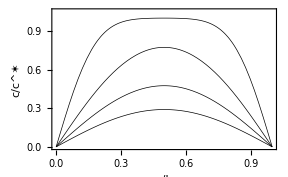

```mathematica
Plot[{g[0.001],g[0.005],g[0.01],g[0.015]},{x,0.,1.},Evaluate[option1]]
```

Fig. Chapter.FigureCaption  Plot of dimensionless concentration profiles described by eqn (Chapter.EquationNumbered). Conditions: D=10^-5cm^2 · s^-1, L=10^-3cm, and (top to bottom) t=0.001, 0.005, 0.01, and 0.015 s.

### Chapter.Section.Subsection Nonhomogeneous Boundary Conditions

Partial differential equations with nonhomogeneous boundary conditions can still be solved using the separation of variables method by first transforming the boundary conditions from nonhomogeneous to homogeneous ones. We begin this example with the boundary conditions

c(0,t)=b_1	for t>0

c(L,t)=b_2	for t>0

with the initial condition

c(x,0)=c^*	for 0≤x≤L

To transform the boundary conditions from nonhomogeneous to homogeneous ones the concentration is considered to be the sum of a steady state concentration s(x), that by definition is independent of time, and a transient concentration u(x, t).

c(x,t)=s(x)+u(x,t)

Taking the second derivative of eqn (Chapter.EquationNumbered) with respect to x gives

(∂^2 c(x,t))/(∂x^2)=(∂^2 s(x))/(∂x^2)+(∂^2 u(x,t))/(∂x^2)

and the first derivative of eqn (Chapter.EquationNumbered) with respect to t gives

(∂c(x,t))/(∂t)=(∂u(x,t))/(∂t)

therefore eqn (Chapter.EquationNumbered) is transformed into the following

(∂u(x,t))/(∂t)=D(∂^2 s(x))/(∂x^2)+D(∂^2 u(x,t))/(∂x^2)

From eqn (Chapter.EquationNumbered) the transformed initial condition and boundary conditions are

s(0)+u(0,t)=b_1	for t>0

s(L)+u(L,t)=b_2	for t>0

s(x)+u(x,0)=c^*	for 0≤x≤L

These conditions can be rewritten alternatively as

s(0)=b_1;  u(0,t)=0	for t>0

s(L)=b_2; u(L,t)=0	for t>0

u(x,0)=c^*-s(x)	for 0≤x≤L

At steady state

(∂c(x,t))/(∂t)=D(∂^2 c(x,t))/(∂x^2)=0

and u(x,t)=0 so that the right hand side of eqn (Chapter.EquationNumbered) can be integrated to obtain the steady state solution.

```mathematica
ClearAll[L];
DSolve[{D[s[x],{x,2}]==0,s[0]== b1,s[L]== b2},s[x],x]
```

{{s[x]→(b1 L-b1 x+b2 x)/L}}

s(x)=b_1+x/L(b_2-b_1)

Since (∂^2 s(x)/∂x^2)=0 eqn (Chapter.EquationNumbered) becomes

(∂u(x,t))/(∂t)=D(∂^2 u(x,t))/(∂x^2)

This equations can be solved using the boundary conditions in eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) and the initial condition in eqn (Chapter.EquationNumbered) that, after substituting eqn (Chapter.EquationNumbered), becomes

u(x,0)=c^*-b_1-x/L(b_2-b_1)	for 0≤x≤L

The problem described by eqns (Chapter.EquationNumbered), (Chapter.EquationNumbered), (Chapter.EquationNumbered) and (Chapter.EquationNumbered) is a homogeneous PDE with homogeneous boundary conditions and can be solved as shown in the previous section. The solution proceeds as described above in §1.3.1 to yield

u(x,t)=∑_(n=1)^∞ A_n exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)	for n=1, 2, 3, …

We now have a distance dependent initial condition, therefore

```mathematica
result2=Solve[(SuperStar[C]-Subscript[b, 1])*∫_0^L Sin[(m*π*x)/L]ⅆx-(Subscript[b, 2]-Subscript[b, 1])*∫_0^L x/L*Sin[(m*π*x)/L]ⅆx==Subscript[A, n]* sinInt[1,1],Subscript[A, n]]/.m-> n
```

{{A_n→-(2 (b_1 n π-b_2 n π Cos[n π]-b_1 Sin[n π]+b_2 Sin[n π]-n π C^*+n π Cos[n π] C^*))/(n^2 π^2)}}

Since n is an integer this can be simplified to:

```mathematica
Simplify[result2,n ∈Integers]
```

{{A_n→-(2 (b_1-(-1)^n b_2+(-1+(-1)^n) C^*))/(n π)}}

Therefore

A_n=2/(n π)[(c^*-b_1)+(b_2-c^*)(-1)^n]

We now have a solution for A_n that can be substituted into eqn (Chapter.EquationNumbered) to give u(x, t)

u(x,t)=2/π∑_(n=1)^∞ 1/n[(c^*-b_1)+(b_2-c^*)(-1)^n]exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)

Having solved for s(x) and u(x,t) in eqns (Chapter.EquationNumbered) and (EquationNumbered) the solutions can substituted into eqn (Chapter.EquationNumbered) to obtain our solution for c(x,t).

c(x,t)=b_1+x/L(b_2-b_1)+2/π∑_(n=1)^∞ 1/n[(c^*-b_1)+(b_2-c^*)(-1)^n]exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)

note

```mathematica
ClearAll[x,n,c^✶,Subscript[b, 1],Subscript[b, 2],𝒟,L,t,g2];

c^✶=1.;
Subscript[b, 1]=0.2;
Subscript[b, 2]=1.;
𝒟=1*^-5;
L=1*^-3;

g2[t_]:=Subscript[b, 1]+x*(Subscript[b, 2]-Subscript[b, 1])+2./π*∑_(n=1)^20 1/n*((c^✶-Subscript[b, 1])-(c^✶-Subscript[b, 2])*Cos[n*Pi])*Sin[n π x]*Exp[-(𝒟 n^2 π^2 t)/L^2]//N;
```

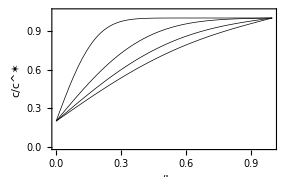

```mathematica
Plot[{g2[0.001],g2[0.005],g2[0.01],g2[0.015]},{x,0.,1.},Evaluate[option1]]
```

Fig. Chapter.FigureCaption Plot of dimensionless concentration profiles described by eqn (Chapter.EquationNumbered). Conditions b_1=0.2, b_2=1.0, D=10^-5 cm^2 · s^-1, L=10^-3cm, and (top to bottom) t=0.001, 0.005, 0.01, and 0.015 s.

### Chapter.Section.Subsection Duhamel’s theorem

Partial differential equations with time varying boundary conditions can be solved using the separation of variables method by first transforming the boundary conditions to homogeneous ones. Consider a potential sweep experiment with a thin layer cell. The boundary conditions for a potential sweep are

c(0,t)=(ξ(t))/(1+ξ(t))=f(t)	for  t>0

c(L,t)=(ξ(t))/(1+ξ(t))=f(t)	for  t>0

where ξ(t)=exp((n F)/(R T)(E_i-υt-E °')) with E_i the initial potential and υ a constant sweep rate. The initial condition is

c(x,0)=c^*	for 0≤x≤L

To solve this problem let’s first consider two functions v(x,t), and u(x,t) that are related to the concentration by

c(x,t) = u(x,t) + v(x,t)

Let the functions v(x,t), and u(x,t) have the following boundary conditions and initial condition

(∂ν(x,t))/(∂t)=(∂^2 ν(x,t))/(∂x^2)

ν(0,t)=(ξ(t))/(1+ξ(t))=f(t)	for  t>0

ν(L,t)=(ξ(t))/(1+ξ(t))=f(t)	for  t>0

ν(x,0)=0	for 0≤x≤L

and

(∂u(x,t))/(∂t)=(∂^2 u(x,t))/(∂x^2)

u(0,t)=0	for  t>0

u(L,t)=0	for  t>0

u(x,0)=c^*	for 0≤x≤L

The solution to eqn (Chapter.EquationNumbered) was given as eqn (Chapter.EquationNumbered). In dimensionless form it is

u(x,t)=(4 c^*)/π∑_(n=1)^∞ 1/n exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)	for odd n

Equation (Chapter.EquationNumbered) can be solved by making use of Duhamel’s theorem. Duhamel’s theorem offers a solution to eqn (Chapter.EquationNumbered), that has time varying boundary conditions, f(t), in terms of another function w(x,t), which is the solution of a PDE that has time independent boundary conditions:

ν(x,t)=∫_0^t (∂w(x,t-z))/(∂t)f(z)ⅆz
=∫_0^t w(x,t-z)f'(z)ⅆz+f(0)w(x,t)

The integral in eqn (Chapter.EquationNumbered) is known as a convolution integral and is discussed further in §1.5.3. The solution for c(x,t) becomes

c(x,t)=u(x,t)+∫_0^t (∂w(x,t-z))/(∂t)f(z)ⅆz

If a new function w(x,t) is defined with the following boundary conditions

w(0,t)=c^*	for  t>0

w(L,t)=c^*	for  t>0

w(x,0)=0	for 0≤x≤L

w(x,t) can be found by separation of variables after first transforming the problem to one with homogeneous boundary conditions as described in §1.3.2 above. The solution is

w(x,t)=c^*-(4 c^*)/π∑_(n=1)^∞ 1/n exp(-(n^2 π^2 D t)/L^2)sin((n π x)/L)	for odd n

therefore

(∂w(x,t-z))/(∂t)=(4 πc^*D)/L^2∑_(n=1)^∞ nexp(-(n^2 π^2 D( t-z))/L^2)sin((n π x)/L)	for odd n

substituting eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) gives

ν(x,t)=∫_0^t (∂w(x,t-z))/(∂t)f(z)ⅆz
=(4 πc^*D)/L^2∑_(n=1)^∞ n exp(-(n^2 π^2 D t)/L^2)sin((n π x)/L)∫_0^t exp((n^2 π^2 D z)/L^2)(ξ(z))/(1+ξ(z))ⅆz

Therefore adding eqns (Chapter.EquationNumbered) and (EquationNumbered) together gives

u(x,t)=(4 c^*)/π∑_(n=1)^∞ 1/n exp((-n^2 π^2 D t)/L^2)sin((n π x)/L)	for odd n

c(x,t)=4 c^*∑_(n=1)^∞ exp(-(n^2 π^2 D t)/L^2)sin((nπ x)/L)(1/(n π)+nπD/L^2∫_0^t exp((n^2 π^2 z)/L^2)(ξ(z))/(1+ξ(z))ⅆz)	for odd n

## Chapter.Section Transforming variables

Chapter.Section.Subsection  Transforming to dimensionless variables

In many cases a difficult to solve PDE can be made easier to solve by transforming the variables. We consider five transformations relevant to electrochemical problems. It is sometimes preferable to convert Fick’s second law to a dimensionless form where possible before attempting a solution. For  t>0 let  t=D t/L^2 therefore ∂t=L^2/D∂t; let x=x/L therefore ∂x^2=L^2∂x^2; and let c(x,t)=c(x,t)/c^*. Making these substitutions the dimensionless equation is

(∂c(x,t))/(∂t)=(∂^2 c(x,t))/(∂x^2)

### Chapter.Section.Subsection Diffusion with a first order chemical reaction

If a first order homogeneous chemical reaction is coupled to the electron transfer reaction eqn (Chapter.EquationNumbered) is replaced by

(∂c(x,t))/(∂t)=(∂^2 c(x,t))/(∂x^2)-k c(x,t)

let

c(x,t)=exp(-k t) u(x,t)

then

(∂c(x,t))/(∂t)=exp(-k t) ((∂u(x,t))/(∂t)-k u(x,t))

and

(∂^2 c(x,t))/(∂x^2)=exp(-k t)(∂^2 u(x,t))/(∂x^2)

By substituting eqns (Chapter.EquationNumbered) to (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) the problem reduces to

```mathematica
ClearAll[u,x,t,k];

D[Exp[-k*t]*u[x,t],t]==D[Exp[-k*t]*u[x,t],{x,2}]-k*Exp[-k*t]*u[x,t]//Simplify
```

ⅇ^(-k t) (u^(0,1)[x,t]-u^(2,0)[x,t])==0

(∂u(x,t))/(∂t)=(∂^2 u(x,t))/(∂x^2)

which is readily solved for u(x,t). The solution for c(x,t) can then be obtained from eqn (Chapter.EquationNumbered). Coupled chemical reactions are considered in Chapter 13.

### Chapter.Section.Subsection The diffusion-convection equation

Consider the following diffusion-convection equation:

(∂c(x,t))/(∂t)=D(∂^2 c(x,t))/(∂x^2)-ν(∂c(x,t))/(∂x)

let

c(x,t)=exp((ν(2x-νt))/(4D))u(x,t)

then

(∂c(x,t))/(∂t)=exp((ν(2x-νt))/(4D))(ν^2/(4D)u(x,t)+(∂u(x,t))/(∂t))

(∂c(x,t))/(∂x)=exp((ν(2x-νt))/(4D))(ν/(2D)u(x,t)+(∂u(x,t))/(∂x))

and

(∂^2 c(x,t))/(∂x^2)=exp((ν(2x-νt))/(4D))(ν^2/(2 D^2)u(x,t)+ν/D(∂u(x,t))/(∂x)+(∂^2 u(x,t))/(∂x^2))

By substituting eqns (Chapter.EquationNumbered) to (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) the problem reduces to

```mathematica
ClearAll[ν,x,𝒟,u,t];

D[Exp[(ν*(2*x-ν*t))/(4*𝒟)]*u[x,t],t]==𝒟*D[Exp[(ν*(2*x-ν*t))/(4*𝒟)]*u[x,t],{x,2}]-ν*D[Exp[(ν*(2*x-ν*t))/(4*𝒟)]*u[x,t],x]//Simplify
```

ⅇ^(-(ν (-2 x+t ν))/(4 𝒟)) (u^(0,1)[x,t]-𝒟 u^(2,0)[x,t])==0

which is readily solved for u(x,t). The solution for c(x,t) can be obtained from eqn (Chapter.EquationNumbered).

### Chapter.Section.Subsection Spherical diffusion

The diffusion equation for diffusion to a spherical surface is given by

(∂c(r,t))/(∂t)=D((∂^2 c(r,t))/(∂r^2)+2/r(∂c(r,t))/(∂r))

If we let

u(r,t)=r c(r,t)

then

(∂u(r,t))/(∂t)=r(∂c(r,t))/(∂t)

and

(∂^2 u(r,t))/(∂r^2)=r(∂^2 c(r,t))/(∂r^2)+2(∂c(r,t))/(∂r)

therefore eqn (Chapter.EquationNumbered) reduces to

```mathematica
ClearAll[r,𝒟,u,t];

D[u[r,t],t]/r==𝒟*(D[u[r,t]/r,{r,2}]+2/r*D[u[r,t]/r,r])//FullSimplify
```

(u^(0,1)[r,t]-𝒟 u^(2,0)[r,t])/r==0

After solving for u(r,t) the solution for c(r,t) is obtained from eqn (Chapter.EquationNumbered).

## Chapter.Section Integral Transform Methods

Chapter.Section.Subsection  Introduction

Integral transforms transform a function f(y) into a new function F(x) with a formula of the kind

F(x)=∫_a^b K(x,y)f(y)ⅆy

where K(x,y) is referred to as the kernel. It is the kernel that distinguishes one type of integral transform from another.

### Chapter.Section.Subsection Laplace transforms

Laplace transforms have historically been the method of choice for electrochemists seeking analytical solutions to problems. The technique transforms PDEs into ordinary differential equations (ODEs) that are solved in a straight forward manner. The inverse transformation yields the solution.
The Laplace transform of a function f(t) is defined as

ℒ{f(t)}=f^-(s)=∫_0^∞ e^(-s t) f(t)ⅆt

The inverse Laplace transform is defined as

ℒ^-1{f^-(s)}=f(t)=1/(2πⅈ)∫_(γ-ⅈ∞)^(γ+ⅈ∞) e^(s t) f^-(s)ⅆs

An important property of the Laplace transform is that it is linear

ℒ{a f(t)+b g(t)}=a f^-(s)+b g^-(s)

Laplace transform of a derivative is readily obtainable using integration by parts and yields:

ℒ{ (d f(t))/(d t)}=s f^-(s)-f(0)

Mathematica can give this result using the function LaplaceTransform.

```mathematica
LaplaceTransform[f'[t],t,s]
```

-f[0]+s LaplaceTransform[f[t],t,s]

For higher order derivatives the Laplace transform of the nth derivative yields:

ℒ{ (d^n f(t))/(d t^n)}=s^n f̄(s)-s^(n-1) f(0)-s^(n-2)d (f(0))/(d t)-s^(n-3)d^2(f(0))/(d t^2)-⋯-(d^(n-1)f(0))/(d t^(n-1))

For example for the fifth derivative

```mathematica
LaplaceTransform[D[f[t],{t,5}],t,s]
```

-s^4 f[0]+s^5 LaplaceTransform[f[t],t,s]-s^3 f'[0]-s^2 f''[0]-s f^(3)[0]-f^(4)[0]

Variables other than time are regarded as constants when doing the transformation therefore

ℒ{ (∂f(x,t))/(∂x)}= (∂f^-(x,s))/(∂x)

```mathematica
LaplaceTransform[D[f[x,t],x],t,s]
```

LaplaceTransform[f^(1,0)[x,t],t,s]

To demonstrate how a solution is obtained with Laplace transforms using Mathematica consider a simple one electron electrochemical reaction occurring under conditions of semi-infinite diffusion. We’ll begin again with Fick’s second law

(∂c(x,t))/(∂t)=D(∂^2 c(x, t))/(∂x^2)

with the initial condition

c(x, 0)=c^*

and boundary condition

c(∞,t)=c^*

The solution begins by taking the Laplace transform of both sides of eqn (Chapter.EquationNumbered) using the function LaplaceTransform. The Laplace transform of c(x,t) with respect to t can be expressed as a function of x, C[s][x].

```mathematica
ClearAll[𝒟,c,c^✶,x,t];

laplaceDemo=LaplaceTransform[D[c[x,t],t]==𝒟*D[c[x,t],{x,2}],t,s]
```

-c[x,0]+s C[s][x]==𝒟 C[s]''[x]

DSolve  may be used to find C[s][x]. The initial boundary condition, c[x,0]→c^✶, is inserted into the previous result using the function ReplaceAll, which is written in shorthand as /.

```mathematica
soln =DSolve[laplaceDemo /. c[x,0] -> c^✶, C[s][x], x]//Simplify
```

{{C[s][x]→c^✶/s+ⅇ^((√s x)/(√𝒟)) C[1]+ⅇ^(-(√s x)/(√𝒟)) C[2]}}

The boundary condition at x → ∞ is then substituted into this solution

```mathematica
soln/. x ->Infinity
```

{{C[s][∞]→c^✶/s+ⅇ^((√s ∞)/(√𝒟)) C[1]+ⅇ^((-∞ √Sign[s])/(√Sign[𝒟])) C[2]}}

The output is not what we expected because the sign of the variables s and D has not been defined. This situation is easily remedied by incorporating the fact that s and D are always positive into a simplification.

```mathematica
Simplify[soln/. x -> Infinity,{s>0,𝒟>0}]
```

{{C[s][∞]→c^✶/s+C[1] ∞}}

For the boundary condition in eqn (Chapter.EquationNumbered) to hold C[1] must equal zero therefore this is inserted back into the result:

```mathematica
soln=soln /. C[1]->0
```

{{C[s][x]→c^✶/s+ⅇ^(-(√s x)/(√𝒟)) C[2]}}

Re-writing this equation in traditional form gives

c^-(x, s)=c^*/s+Bexp[-(x(s/D))^(1/2)]

where B, i.e. C[1], is a constant that is evaluated from the second boundary condition. To continue on let’s consider a potential step to the limiting current region where the second boundary condition is

c(0,t)=0		 t>0

Applying this boundary condition gives

```mathematica
soln/.x-> 0
```

{{C[s][0]→c^✶/s+C[2]}}

Therefore C[2]=-c^*/s. Substituting this back gives

```mathematica
soln2=soln /. C[2]->-c^✶/s
```

{{C[s][x]→c^✶/s-(c^✶ ⅇ^(-(√s x)/(√𝒟)))/s}}

The solution for c(x,t) is obtained from taking the inverse Laplace transform of C[s][x] using InverseLaplaceTransform.

```mathematica
soln3= InverseLaplaceTransform[soln2⟦1,1,2⟧, s, t]
```

ConditionalExpression[c^✶-c^✶ Erfc[x/(2 √(t 𝒟))], x √𝒟>0]

The assumptions required are that x≥0, t>0, and D>0 and these assumptions can be added when undertaking the inverse transform.

```mathematica
finalResult=Assuming [{x>0,t>0,𝒟>0},InverseLaplaceTransform[soln2⟦1,1,2⟧, s, t]]
```

c^✶-c^✶ Erfc[x/(2 √(t 𝒟))]

The result is a concentration profile that is described by an error function (see also functions.wolfram.com). The calculated concentration profiles for several values of t are shown in Fig. Chapter.FigureCaption.

```mathematica
ClearAll[x,c^✶,𝒟,t,c];
c^✶=1.;
𝒟=10.^-5;
c[x_,t_]:=c^✶ Erf[x/(2 √(t*𝒟))];
```

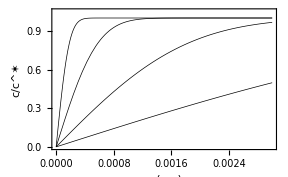

```mathematica
laplacePlot=Plot[{c[x,0.001],c[x,0.01],c[x,0.1],c[x,1.0]},{x,0.,0.003},Evaluate[option2]]
```

Fig. Chapter.FigureCaption  Plot of concentration profiles for a potential step to the limiting current region after (top to bottom) t =0.001, 0.01, 0.1, and 1.0 s.

### Chapter.Section.Subsection Numerical inversion of Laplace transforms

On many occasions you may find that Mathematica cannot perform the inverse transform. For example if the solution is an infinite sum then InverseLaplaceTransform will be unable to do the inversion. When you find that you cannot obtain the inverse transform it is helpful to have a set of table of Laplace transforms to refer to. Occasionally you may find that you cannot find the inverse transform from tables. Rather than abandon the Laplace transform method for another method of solution you may want to consider performing a numerical inversion of the transform using one of the built-in method options. As a conclusion to this section the numerical inversion is compared to the direct inversion for the example just discussed.

```mathematica
ClearAll[x,c^✶,𝒟,t,c,s];

c^✶=1.;
𝒟=1*^-5;
numInv[x_,t_]:=InverseLaplaceTransform[c^✶/s-(c^✶ ⅇ^(-(√s x)/(√𝒟)))/s,s,t,Method->"Stehfest"]
```

A comparison between the analytical result and the numerical inversion is shown in Fig. Chapter.FigureCaption .

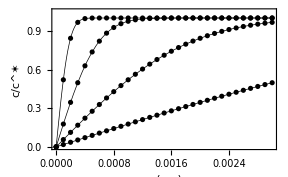

```mathematica
ClearAll[plot1,plot2,plot3,plot4];

plot1=ListPlot[Table[{x,numInv[x,0.001]},{x,0,0.003,0.0001}]];
plot2=ListPlot[Table[{x,numInv[x,0.01]},{x,0,0.003,0.0001}]];
plot3=ListPlot[Table[{x,numInv[x,0.1]},{x,0,0.003,0.0001}]];
plot4=ListPlot[Table[{x,numInv[x,1.0]},{x,0,0.003,0.0001}]];

Show[laplacePlot,plot1,plot2,plot3,plot4]
```

Fig. Chapter.FigureCaption  Plot of concentration profiles for a potential step to the limiting current region after (top to bottom) t =0.001, 0.01, 0.1, and 1.0 s. Lines - inverse of the Laplace transform; points - numerical inversion of Laplace transform.

### Chapter.Section.Subsection The convolution integral

The inverse transform of the product of two transformed functions f(s) and g(s) can be obtained by using the convolution theorem. The version of the convolution integral applicable to electrochemistry requires that for t<0 both f(0)=0 and g(0)=0. The convolution theorem is:

ℒ^-1{f^-(s)g^-(s)}=∫_0^t f(t-z)g(z)ⅆz
=∫_0^t f(z)g(t-z)ⅆz

The convolution integral is often written in the literature as f(s)*g(s). Differentiation of the convolution integral gives:

∂/(∂t)[f(t)*g(t)]=(∂f(t))/(∂t)*g(t)=f(t)*(∂g(t))/(∂t)

If f and g are also functions of distance, x, i.e. f(x,t)*g(x,t), differentiation with respect to distance yields:

∂/(∂x)[f(x,t)*g(x,t)]=(∂f(x,t))/(∂x)*g(x,t)=f(x,t)*(∂g(x,t))/(∂x)

If only one of the functions depends on distance differentiation yields:

∂/(∂x)[f(x,t)*g(t)]=(∂f(x,t))/(∂x)*g(t)

## Chapter.Section Summary

In this chapter several methods of finding analytical solutions to PDEs were discussed and examples of implementing the solution in Mathematica were given. In cases where no analytical solution exists numerical methods must be used to obtain a solution. In the next three chapters various finite difference numerical methods are explained and detailed implementation of these methods using Mathematica are discussed.